# Deriving the empirical correlation function and fitting a curve to it

## Translating from “Towards a unified descriptive theory for spatial ecology” (who only provide a PDF of their Mathematica notebook!)

M Scott & M Osmond
2016 January 21

## Method with random data

Define the spatial extent of the area of interest (e.g., Barro Colorado Island)

```mathematica
{Lx,Ly}={1000,500}; (*total x and y distance of area of interest, ie a grid with length Lx and width Ly*)
Asub=100;(*space between coordinates, ie we chop up the total area into squares with length Asub; best if this divides the total space nicely, ie Lx/Asub and Ly/Asub are integers*)
```

Make up the data (because the authors suck at making it available)

```mathematica
numplots=10000;(*number of plots/datapoints*)
data=Table[{{RandomVariate[UniformDistribution[{0,Lx}]],RandomVariate[UniformDistribution[{0,Ly}]]},RandomInteger[{1,3}],RandomInteger[10]},{i,1,numplots}];
(*(x,y) locations of each plot, species code of each plot,abundance of that species in each plot*)
```

Get each variable of interest from data table

```mathematica
gx=Table[Transpose[data][[1]][[i,1]],{i,1,numplots}]; (*x coordinates of all plots*)
gy=Table[Transpose[data][[1]][[i,2]],{i,1,numplots}]; (*y coordinates of all plots*)
sp=Transpose[data][[2]];(*species code for each plot*)
ab=Transpose[data][[3]];(*species abundance at each plot*)
```

Some summary statistics of the data

```mathematica
Uspecie=Union[sp];(*vector of species IDs*)
Nspecies=Length[Uspecie];(*total number of species*)
TotAbundance=Total[ab];(*total abundance, across all species*)
```

Defining the coordinate system of the area

```mathematica
allpos=Tuples[{Range[Lx/Asub],Range[Ly/Asub]}]; (*coordinates, in translated form, ie. {1,1}, {1,2}, ..., {2,1}, {2,2}, ..., {m,n}*)
xyCpos=Flatten[Table[{(2 i+1)/2,(2 j+1)/2}// N,{i,0,(Lx/Asub)-1,1},{j,0,(Ly/Asub)-1,1}],1];(*halfway points between coordinates, which we use later to derive the distances between centers of each "bin" (area below (south) and to left (west) of each coordinate*)
allpair=Tuples[{allpos,allpos}];(*pairs of each translated coordinate with each other, e.g., {{1,1},{1,1}}*)
nplot=Range[Length[allpos]]; (*total number of coordinates/bins*)
```

Locations of plots (the bin they are in)

```mathematica
Xpos[p_]:=Flatten[Position[gx,x_?(Asub*(p-1) ≤ #<Asub*p&)],1](*which plots (their position in the data vector) have x location between two coordinates, for all pairs of x coordinates; for p between 1 and Lx/Asub*)
Ypos[q_]:=Flatten[Position[gy,x_?(Asub*(q-1) ≤ #<Asub*q&)],1](*which plots have y location between two coordinates, for all pairs of y coordinates; for q between 1 and Ly/Asub*)
rule1=Flatten[Table[{allpos[[i]] -> nplot[[i]]},{i,1,Length[allpos]}],1];(*translate from coordinates (tuple) to single identifying number*)
rule2=Flatten[Table[{nplot[[i]] -> allpos[[i]]},{i,1,Length[allpos]}],1];(*translate back*)
XYpos[{p_,q_}]:=Intersection[Xpos[p],Ypos[q]];(*which plots have location (x,y) within (x(p-1),x p) and (y(p-1), y p)*)
possub=ParallelMap[XYpos,allpos];(*which plots fall in which bin (e.g., (x,y)=(321,434), with Asub=100, would fall in (400,500)*)
```

Which species are where

```mathematica
XYS[i_]:=Transpose[{gx[[possub[[i]]]],gy[[possub[[i]]]],sp[[possub[[i]]]]}];(*gives (x,y) location of plots, and sp code, in each bin*)
SabA[i_]:=Count[sp[[possub[[i]]]],#]&/@ Uspecie (*number of plots with each species in each bin*)
SA[i_]:=Boole/@ (MemberQ[sp[[possub[[i]]]],#]&/@ Uspecie) (*1 if at least one plot with a species in given bin, ie presence/absence in bin*)
Spos=Table[SA[i],{i,1,Length[possub]}];(*table with all bins*)
```

Covariance in species abundance by distances

```mathematica
dist[{i_,j_}]:=Sqrt[Total[(Abs[xyCpos[[i]]-xyCpos[[j]]])^2]] (*Euclidean distance between center of two bins (in translated space; need to multiply by Asub to get real distances, which we do later)*)
index[{i_,j_}]:={i,j}(*not sure what this does, but doesnt hurt*)
alldist=Map[dist,allpair/.rule1]; (*distance between center of all pairs of bins*)
rvec=Union[alldist];(*all unique distances in increasing order*)
indexpair=Map[index,allpair/. rule1];(*translate from tuples of coordinates to pairs of coordinate indices*)
posdist=Position[alldist,#]&/@ rvec;(*identify coordinate index pairs whose bin centers are given distance apart*)
Cov[{i_,j_}]:=Mean[SabA[i] SabA[j]]/(Mean[SabA[i]] Mean[SabA[j]])//N;(*"covariance" in number of plots with species across bins, note that the "covariance" is taken over all species, ie "covariance" in community composition*)
allcov=ParallelTable[Map[Cov,indexpair[[Flatten[posdist[[i]],1]]]],{i,1,Length[rvec]}];(*covaraiance in number of plots with species at each distance*)
```

Our empirical correlation function

```mathematica
empPCF=Transpose[{rvec*Asub,Map[Mean,allcov]}];(*empirical correlation function, PCF; first element of each pair is the (untranslated) distance between the center of two bins (rvec*Asub), the second element is the mean covariance in number of plots with species across all pairs of bins that distance apart*)
```

which looks like this

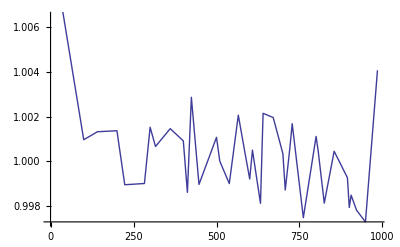

```mathematica
ListPlot[empPCF,Joined->True]
```

Fitting the function to the data

```mathematica
g[r_]:=1+1/(2π)(ρ/λ)^2 BesselK[0,r/λ](*function to fit to the empirical PCF*)
λ=.;(*what does this do?*)
ρ=.;
fitcor=NonlinearModelFit[Rest[empPCF],g[r],{{λ,10^9},{ρ,0.1}},r];(*fit the function, with some parameter guesses*)
```

NonlinearModelFit::nrlnum: The function value {-0.000964021 - 9.12302×10^-20\ ⅈ, -0.00132155 - 9.12302×10^-20\ ⅈ, -0.00136589 - 9.12302×10^-20\ ⅈ, 0.0010546  - 9.12302×10^-20\ ⅈ, 0.00099854  - 9.12302×10^-20\ ⅈ, « 27 », 0.00207404  - 9.12302×10^-20\ ⅈ, 0.00152313  - 9.12302×10^-20\ ⅈ, 0.00219602  - 9.12302×10^-20\ ⅈ, 0.00271943  - 9.12302×10^-20\ ⅈ, -0.00407493 - 9.12302×10^-20\ ⅈ} is not a list of real numbers with dimensions {37} at {λ, ρ} = {-5.93093×10^8, 0.253342}.

How good is the fit?

```mathematica
Grid[Transpose[{#,fitcor[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment -> Left](*stats for fit*)
```

AdjustedRSquared | 0.999997
AIC | -364.97
BIC | -360.138
RSquared | 0.999997

What are our parameter estimates?

```mathematica
fitcor["ParameterTable"](*stats for parameter estimates*)
σλ1=fitcor["ParameterTableEntries"][[1,2]];(*standard error for lambda*)
σρ1=fitcor["ParameterTableEntries"][[2,2]];(*standard error for rho*)(*standard error for rho*)
```

| Estimate | Standard Error | t-Statistic | P-Value
λ | -5.93093×10^8 | 1.47629×10^26+6.19388×10^17 ⅈ | -4.01744×10^-18+1.68554×10^-26 ⅈ | 1.+2.0615×10^-22 ⅈ
ρ | 0.253342 | 6.09264×10^16-4.77165×10^14 ⅈ | 4.15791×10^-18+3.2564×10^-20 ⅈ | 1.-2.91504×10^-19 ⅈ

Or if you like confidence intervals better...

```mathematica
fitcor["ParameterConfidenceIntervalTable"](*get confidence intervals too*)
```

| Estimate | Standard Error | Confidence Interval
λ | -5.93093×10^8 | 1.47629×10^26+6.19388×10^17 ⅈ | {-2.99704×10^26-1.25742×10^18 ⅈ,2.99704×10^26+1.25742×10^18 ⅈ}
ρ | 0.253342 | 6.09264×10^16-4.77165×10^14 ⅈ | {-1.23687×10^17+9.68697×10^14 ⅈ,1.23687×10^17-9.68697×10^14 ⅈ}

Plot fitted curve with data points

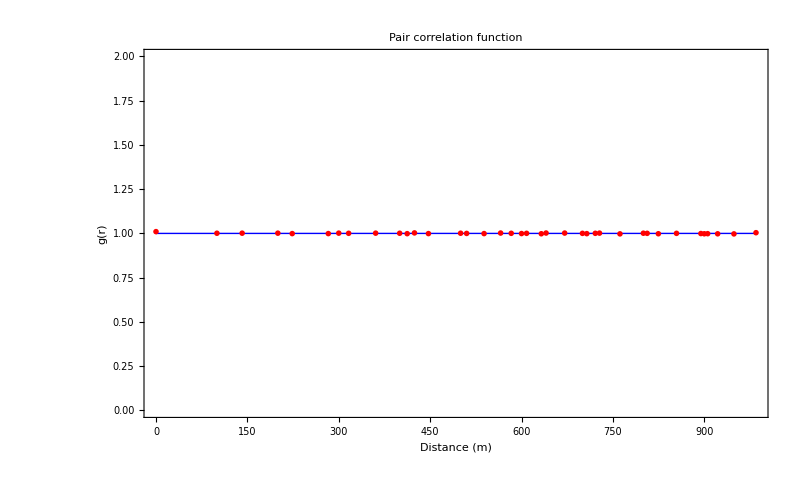

```mathematica
Plot[
fitcor[r],
{r,Min[rvec*Asub],Max[rvec*Asub]},
PlotStyle->{ Blue,Thick},
PlotRange->{{0,Max[rvec*Asub]},Automatic},
Frame ->{{True,False},{True,False}},
FrameLabel -> {"Distance (m)","g(r)"},
PlotLabel -> "Pair correlation function",
LabelStyle -> {FontFamily -> "Times",FontSize -> 12},
Prolog -> {Red,PointSize[0.005],Point/@ empPCF},
Axes->False,
ImageSize->800
]
```

Plot fitted curve with confidence bands

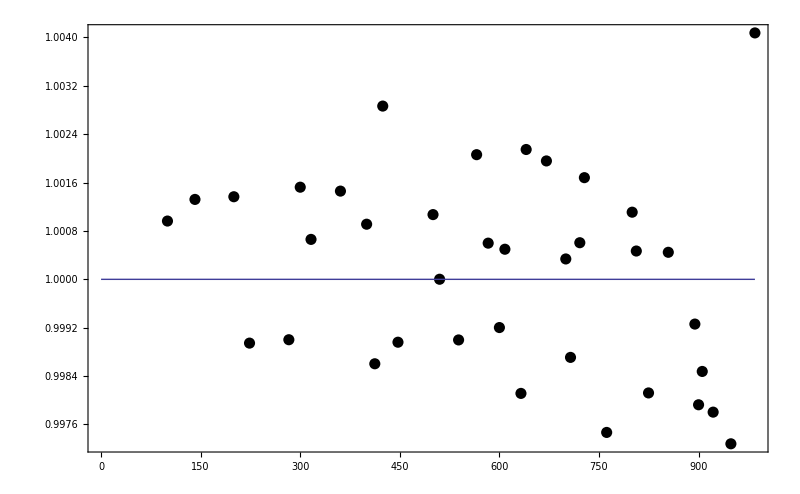

```mathematica
{bands90[x_],bands95[x_],bands99[x_],bands999[x_]} =Table[fitcor["MeanPredictionBands",ConfidenceLevel -> cl],{cl,{.9,.95,.99,.999}}];(*confidence bands*)
Show[
ListPlot[Rest[empPCF],PlotStyle->{Black,PointSize[0.01]},Axes->False],Plot[{fitcor[r],bands90[r],bands95[r],bands99[r],bands999[r]},{r,Min[rvec*Asub],Max[rvec*Asub]},Filling-> {2 ->{1},3 ->{2},4 ->{3},5 ->{4}}],
PlotRange->{{0,Max[rvec*Asub]},Automatic},
Frame->{True,True,False,False},
ImageSize->800]
```

## Simulated Data

Load data from Patrick’s simulation

```mathematica
datadir="/Users/mmosmond/Documents/PHD/PCFinR/";
simdata=Import[datadir<>"SimulatedAbundances"<>".csv"];
```

The data comes with 5 columns

```mathematica
simdata[[1]]
```

{x,y,Species,Abundance,Stress_abund}

x is the x location (1:20) y is the y location (1:20), species is species ID (1:80), abundance is number of individuals of that species in plot, and stress abundance is abundance under some stressor (we will eventually want to compare model results with and without stressor).

We first drop the column names

```mathematica
simdata=Drop[simdata,{1}];
```

Define the spatial extent of the area of interest

```mathematica
{Lx,Ly}={20,20}; (*total x and y distance of area of interest, ie a grid with length Lx and width Ly*)
Asub=5;(*space between coordinates, ie we chop up the total area into squares with length Asub; best if this divides the total space nicely, ie Lx/Asub and Ly/Asub are integers*)
```

Get each variable of interest from data table

```mathematica
gx=Transpose[simdata][[1]];
gy=Transpose[simdata][[2]];
sp=Transpose[simdata][[3]];
ab=Transpose[simdata][[4]];
stab=Transpose[simdata][[5]];
```

Some summary statistics of the data

```mathematica
Uspecie=Union[sp];(*vector of species IDs*)
Nspecies=Length[Uspecie];(*total number of species*)
TotAbundance=Total[ab];(*total abundance, across all species*)
```

Defining the coordinate system of the area

```mathematica
allpos=Tuples[{Range[Lx/Asub],Range[Ly/Asub]}]; (*coordinates, in translated form, ie. {1,1}, {1,2}, ..., {2,1}, {2,2}, ..., {m,n}*)
xyCpos=Flatten[Table[{(2 i+1)/2,(2 j+1)/2}// N,{i,0,(Lx/Asub)-1,1},{j,0,(Ly/Asub)-1,1}],1];(*halfway points between coordinates, which we use later to derive the distances between centers of each "bin" (area below (south) and to left (west) of each coordinate*)
allpair=Tuples[{allpos,allpos}];(*pairs of each translated coordinate with each other, e.g., {{1,1},{1,1}}*)
nplot=Range[Length[allpos]]; (*total number of coordinates/bins*)
```

Locations of plots (the bin they are in)

```mathematica
(*Xpos[p_]:=Flatten[Position[gx,x_?(Asub*(p-1) ≤ #<Asub*p&)],1]*)
Xpos[p_]:=Flatten[Position[gx,x_?(Asub*(p-1) <#≤ Asub*p&)],1]
(*which plots (their position in the data vector) have x location between two coordinates, for all pairs of x coordinates; for p between 1 and Lx/Asub*)
(*Ypos[q_]:=Flatten[Position[gy,x_?(Asub*(q-1) ≤ #<Asub*q&)],1]*)
Ypos[q_]:=Flatten[Position[gy,x_?(Asub*(q-1)<#≤Asub*q&)],1]
(*which plots have y location between two coordinates, for all pairs of y coordinates; for q between 1 and Ly/Asub*)
rule1=Flatten[Table[{allpos[[i]] -> nplot[[i]]},{i,1,Length[allpos]}],1];(*translate from coordinates (tuple) to single identifying number*)
rule2=Flatten[Table[{nplot[[i]] -> allpos[[i]]},{i,1,Length[allpos]}],1];(*translate back*)
XYpos[{p_,q_}]:=Intersection[Xpos[p],Ypos[q]];(*which plots have location (x,y) within (x(p-1),x p) and (y(p-1), y p)*)
possub=ParallelMap[XYpos,allpos];(*which plots fall in which bin (e.g., (x,y)=(321,434), with Asub=100, would fall in (400,500)*)
```

Which species are where

```mathematica
XYS[i_]:=Transpose[{gx[[possub[[i]]]],gy[[possub[[i]]]],sp[[possub[[i]]]]}];(*gives (x,y) location of plots, and sp code, in each bin*)
(*SabA[i_]:=Count[sp[[possub[[i]]]],#]&/@ Uspecie*) (*number of plots with each species in each bin*)
(*SabA[i_]:=(Count[sp[[possub[[i]]]],#]&/@ Uspecie)*ab[[possub[[i]]]]*)(*number of plots of each species in each bin*)
SabA[i_]:=Table[Sum[ab[[possub[[i]]]][[k]],{k,Flatten[(Position[sp[[possub[[1]]]],#]&/@ Uspecie)[[j]]]}],{j,1,Dimensions[Uspecie][[1]]}] (*number of plots * abundance in that plot of each species in each bin*)
(*SA[i_]:=Boole/@ (MemberQ[sp[[possub[[i]]]],#]&/@ Uspecie) *)(*1 if at least one plot with a species in given bin, ie presence/absence in bin*)
SA[i_]:=Boole[#>0]&/@SabA[1]
Spos=Table[SA[i],{i,1,Length[possub]}];(*table with all bins*)
```

Covariance in species abundance by distances (allcov takes a while to run)

```mathematica
dist[{i_,j_}]:=Sqrt[Total[(Abs[xyCpos[[i]]-xyCpos[[j]]])^2]] (*Euclidean distance between center of two bins (in translated space; need to multiply by Asub to get real distances, which we do later)*)
index[{i_,j_}]:={i,j}(*not sure what this does, but doesnt hurt*)
alldist=Map[dist,allpair/.rule1]; (*distance between center of all pairs of bins*)
rvec=Union[alldist];(*all unique distances in increasing order*)
indexpair=Map[index,allpair/. rule1];(*translate from tuples of coordinates to pairs of coordinate indices*)
posdist=Position[alldist,#]&/@ rvec;(*identify coordinate index pairs whose bin centers are given distance apart*)
Cov[{i_,j_}]:=Mean[SabA[i] SabA[j]]/(Mean[SabA[i]] Mean[SabA[j]])//N;(*"covariance" in number of plots with species across bins, note that the "covariance" is taken over all species, ie "covariance" in community composition*)
allcov=Table[ParallelMap[Cov,indexpair[[Flatten[posdist[[i]],1]]]],{i,1,Length[rvec]}];(*covariance in number of plots with species at each distance*)
```

Our empirical correlation function

```mathematica
empPCF=Transpose[{rvec*Asub,Map[Mean,allcov]}];(*empirical correlation function, PCF; first element of each pair is the (untranslated) distance between the center of two bins (rvec*Asub), the second element is the mean covariance in number of plots with species across all pairs of bins that distance apart*)
```

which looks like this

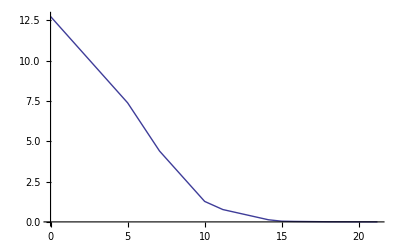

```mathematica
ListPlot[empPCF,Joined->True]
```

```mathematica
empPCFNoZero=Drop[empPCF,1]
```

{{5.,7.39011},{7.07107,4.39919},{10.,1.27118},{11.1803,0.765904},{14.1421,0.131117},{15.,0.0435169},{15.8114,0.0291982},{18.0278,0.00858864},{21.2132,0.00130362}}

Fitting the function to the data

```mathematica
g[r_]:=1+1/(2π)(ρ/λ)^2 BesselK[0,r/λ](*function to fit to the empirical PCF*)
λ=.;(*what does this do?*)
ρ=.;
fitcor=NonlinearModelFit[Rest[empPCF],g[r],{{λ,2},{ρ,50}},r];(*fit the function, with some parameter guesses*)
```

How good is the fit?

```mathematica
Grid[Transpose[{#,fitcor[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment -> Left](*stats for fit*)
```

AdjustedRSquared | 0.88983
AIC | 28.6514
BIC | 29.2431
RSquared | 0.914312

What are our parameter estimates?

```mathematica
fitcor["ParameterTable"](*stats for parameter estimates*)
σλ1=fitcor["ParameterTableEntries"][[1,2]];(*standard error for lambda*)
σρ1=fitcor["ParameterTableEntries"][[2,2]];(*standard error for rho*)(*standard error for rho*)
```

| Estimate | Standard Error | t-Statistic | P-Value
λ | 2.45631 | 0.942178 | 2.60706 | 0.0350631
ρ | 48.0522 | 6.5506 | 7.33554 | 0.000157872

Or if you like confidence intervals better...

```mathematica
fitcor["ParameterConfidenceIntervalTable"](*get confidence intervals too*)
```

| Estimate | Standard Error | Confidence Interval
λ | 2.45631 | 0.942178 | {0.228416,4.68421}
ρ | 48.0522 | 6.5506 | {32.5625,63.5419}

Plot fitted curve with data points

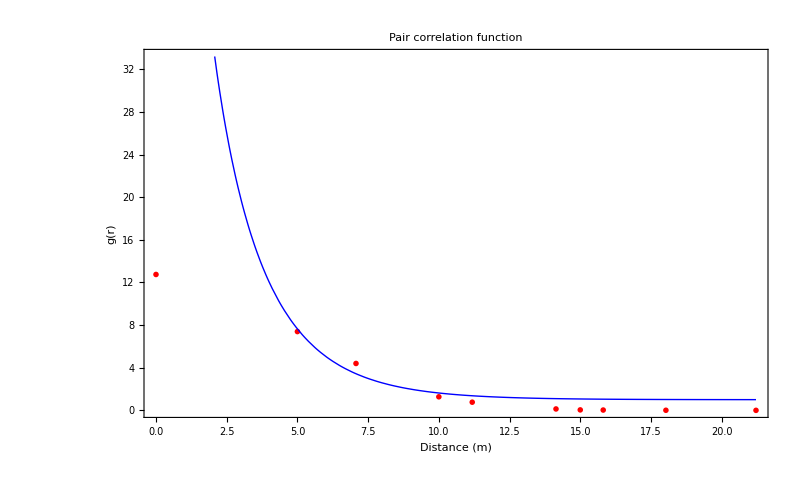

```mathematica
Plot[
fitcor[r],
{r,Min[rvec*Asub],Max[rvec*Asub]},
PlotStyle->{ Blue,Thick},
PlotRange->{{0,Max[rvec*Asub]},Automatic},
Frame ->{{True,False},{True,False}},
FrameLabel -> {"Distance (m)","g(r)"},
PlotLabel -> "Pair correlation function",
LabelStyle -> {FontFamily -> "Times",FontSize -> 12},
Prolog -> {Red,PointSize[0.005],Point/@ empPCF},
Axes->False,
ImageSize->800
]
```

Plot fitted curve with confidence bands

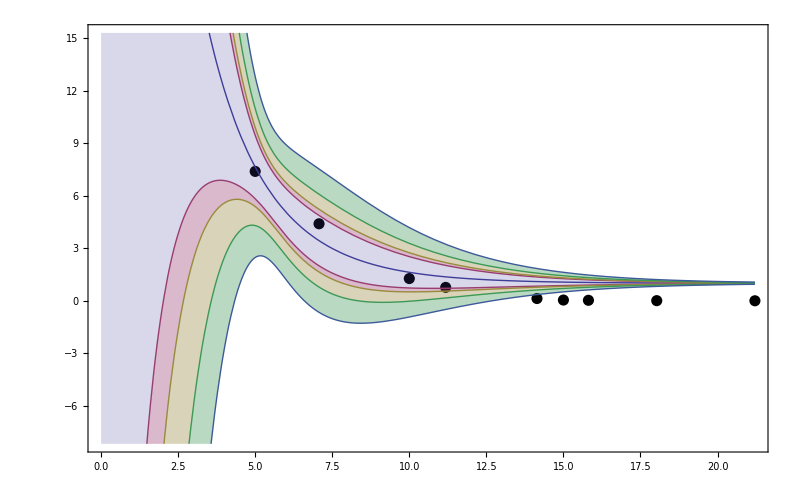

```mathematica
{bands90[x_],bands95[x_],bands99[x_],bands999[x_]} =Table[fitcor["MeanPredictionBands",ConfidenceLevel -> cl],{cl,{.9,.95,.99,.999}}];(*confidence bands*)
Show[
ListPlot[Rest[empPCF],PlotStyle->{Black,PointSize[0.01]},Axes->False],Plot[{fitcor[r],bands90[r],bands95[r],bands99[r],bands999[r]},{r,Min[rvec*Asub],Max[rvec*Asub]},Filling-> {2 ->{1},3 ->{2},4 ->{3},5 ->{4}}],
PlotRange->{{0,Max[rvec*Asub]},{0,Automatic}},
Frame->{True,True,False,False},
ImageSize->800]
```

## Plotting functions

```mathematica
ind=Table[Total[SabA[i]],{i,1,Max[nplot]}];(*number of individuals in each plot*)
```

```mathematica
λ=.;
ρ=.;
ν=.;
α=.;
β=.;
α2p[L_]:=π (L/ρ)^2(1-(2λ)/L(BesselK[1,L/λ]BesselI[1,L/λ])/(BesselK[1,L/λ]BesselI[0,L/λ] + BesselK[0,L/λ]BesselI[1,L/λ]))^-1;
β2[L_]:=(Total[ind]/(Nspecies*Lx*Ly))*ρ^2(1-(2λ)/L(BesselK[1,L/λ]BesselI[1,L/λ])/(BesselK[1,L/λ]BesselI[0,L/λ] + BesselK[0,L/λ]BesselI[1,L/λ]));
rsapres2medp[n_,L_]:=CDF[GammaDistribution[α2p[L],β2[L]],2^(n+1)]-CDF[GammaDistribution[α2p[L],β2[L]],2^n];
sarmedp[L_]:=1-CDF[GammaDistribution[α2p[L],β2[L]],1];
SAR[r_]:=Nspecies*sarmedp[r]/sarmedp[ ((Lx*Ly)/π)^(1/2)]/.fitcor["BestFitParameters"];
SAD[n_,r_]:=Nspecies*rsapres2medp[n,r]/sarmedp[ ((Lx*Ly)/π)^(1/2)]/.fitcor["BestFitParameters"];
upRichness=NsppSamp*(sarmedp [((Lx*Ly)/π)^(1/2),dens,λ,ρ])/(sarmedp [((samp*Asp)/π)^(1/2),dens,λ,ρ]);
UPdens=NSpecies*dens/upRichness;
downSAR[r_]:=upRichness*sarmedp[r,UPdens,λ,ρ]/sarmedp[((Lx*Ly)/π)^(1/2),UPdens,λ,ρ];
```

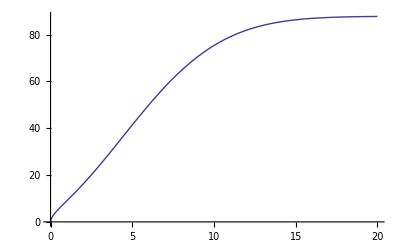

```mathematica
Plot[SAR[r],{r,0,20}]
```